### Fourier Transform of sine - Gaussian

Define Functions

```mathematica
sineGaussian=A/(√(2π)σ) ⅇ^((-(t-Subscript[f, c])^2)/(2 σ^2))Sin[2π Subscript[f, c] t]
```

(A ⅇ^(-(t-f_c)^2/(2 σ^2)) Sin[2 π t f_c])/(√(2 π) σ)

```mathematica
FT=Abs[(√2)/(√T)∫_-T^T (sineGaussian ⅇ^(2π f ⅈ t))ⅆt]
```

1/(2 √2)ⅇ^(-2 π Re[f^2 π σ^2+f (-ⅈ+2 π σ^2) f_c+π σ^2 f_c^2]) Abs[1/(√T)A (ⅇ^(2 π (4 f π σ^2-ⅈ f_c) f_c) (Erf[(T+2 ⅈ π σ^2 (f-f_c)+f_c)/(√2 σ)]+Erf[(T-2 ⅈ f π σ^2+(-1+2 ⅈ π σ^2) f_c)/(√2 σ)])-ⅇ^(2 ⅈ π f_c^2) (Erf[(T-f_c-2 ⅈ π σ^2 (f+f_c))/(√2 σ)]+Erf[(T+f_c+2 ⅈ π σ^2 (f+f_c))/(√2 σ)]))]

Define constants

```mathematica
T=250;Subscript[f, c]=15;Q=1;σ=(2 π Subscript[f, c])/Q;A=10;
```

Plot  time-series

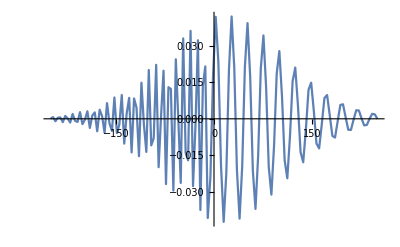

```mathematica
Plot[Evaluate[sineGaussian/.{A->A,Subscript[f, c]->Subscript[f, c],σ->σ}],{t,-T,T},PlotRange->All,PlotPoints->3]
```

If I copy the output of typing FT[f] and turn it into a new function, and plot the new function, it is significantly faster than just plotting FT[g] - this takes much longer.

Plot Fourier Transform

```mathematica
LogLogPlot[Evaluate[FT/.{T->T,A->A,Subscript[f, c]->Subscript[f, c],σ->σ}],{f,1,1000},PlotRange->Full]
```

General::munfl: Exp[-4.48869×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.57405×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.67333×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Evaluate[FT/.{T->T,A->A,Subscript[f, c]->Subscript[f, c],σ->σ,f->3.0}]
```

General::munfl: Exp[-779.273] is too small to represent as a normalized machine number; precision may be lost.

0.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at t = ∞.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in t in the region {{-∞,∞}}. NIntegrate obtained 0.+0. ⅈ and 0. for the integral and error estimates.

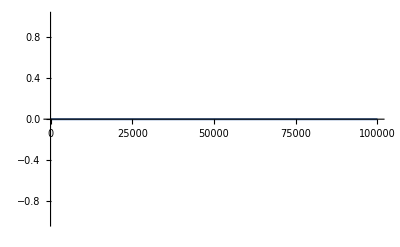

```mathematica
Plot[FourierTransform[sineGaussian/.{A->A,Subscript[f, c]->Subscript[f, c],σ->σ},t,f],{f,0,10^5}]
```